## Basic CR model

### Initialize constants

Set number of consumers, resources, and enzyme budget

```mathematica
m=5;
p=3;
```

Define constants for each consumer

```mathematica
c=#&/@RandomReal[{0,1},{m,p}]
```

{{0.310704,0.572252,0.813646},{0.409036,0.666526,0.45285},{0.358011,0.930285,0.881993},{0.417952,0.0653316,0.760531},{0.427835,0.298107,0.474578}}

```mathematica
g=Table[1,m,p]
```

{{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1}}

```mathematica
z=Table[0.1,m]
```

{0.1,0.1,0.1,0.1,0.1}

Define constants for each resource

```mathematica
κ=Table[0.3,p]
```

{0.3,0.3,0.3}

```mathematica
μ=Table[0,p]
```

{0,0,0}

### Initialize populations

```mathematica
r0=Table[1,p]
```

{1,1,1}

```mathematica
n0=Table[1,m]
```

{1,1,1,1,1}

### Solve The differential equations

```mathematica
sols=NDSolve[{
r[0]==r0,
r'[t]==κ-μ*r[t]-r[t]*n[t].c,
n[0]==n0,
n'[t]==n[t]*(r[t].Transpose[c*g]-z)
},
{r,n},
{t,0,10000}][[1]];
```

### Plot dynamics

```mathematica
sols
```

{r→InterpolatingFunction[…],n→InterpolatingFunction[…]}

```mathematica
Show[Plot3D[1-x-y,{x,0,1},{y,0,1},PlotStyle->Directive[Opacity[0.3]]],ListPointPlot3D[List/@c],ListPointPlot3DAspectRatio->1]
```

-Graphics3D-

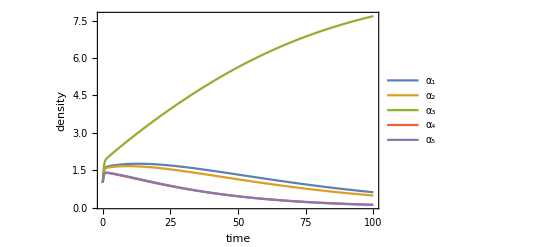

```mathematica
Plot[Evaluate[Table[Indexed[n[t],a]/.sols,{a,m}]],{t,0,100},PlotRange->{All,{0,All}},Frame->True,FrameLabel->{"time","density"},PlotLegends->{"α_1","α_2","α_3","α_4","α_5"}]
```

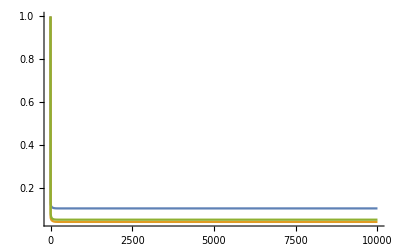

```mathematica
Plot[Evaluate[Table[Indexed[r[t],j]/.sols,{j,p}]],{t,0,10000},PlotRange->{All,{0,All}}]
```

### Equilibrium state

```mathematica
crSteadyState[{n0_,c_,g_,z_},r0_,κ_,μ_,tMax_:10000000]:=
NDSolveValue[{
r[0]==r0,
r'[t]==κ-μ*r[t]-r[t]*n[t].c,
n[0]==n0,
n'[t]==n[t]*(r[t].Transpose[c*g]-z)
},
n,
{t,0,tMax}][tMax]
```

```mathematica
crSteadyState[{n0,c,g,z},r0,κ,μ]
```

{9.27161×10^-39,9.,9.37296×10^-40,-5.44884×10^-49,2.37567×10^-41}

## HGT

Mutate one of the vectors and change all the corresponding vectors

```mathematica
(*Input: each of the variables involving α 
Output: each of the updated variables*)
```

```mathematica
mutate[{n0_,c0_,g0_,z0_}]:=
	Module[{n=n0,c=c0,g=g0,z=z0,p=Length[c[[1]]],mutation},
		mutation=ReplacePart[
			ConstantArray[0,p],
			RandomInteger[{1,p}]->RandomVariate[NormalDistribution[0,0.1]]];
		AppendTo[c,Ramp[RandomChoice[Ramp[n]->c]+mutation]];
		AppendTo[n,0.1];
		AppendTo[g,Table[1,p]];
		AppendTo[z,0.1];
		{n,c,g,z}
	]
```

```mathematica
mutate[{n0,c,g,z}]
```

{{1,1,1,1,1,0.1},{{0.0889142,0.578254,0.89649},{0.325809,0.848952,0.671086},{0.491914,0.511325,0.175811},{0.133059,0.350979,0.321668},{0.397253,0.609535,0.0862465},{0.491914,0.511325,0.00310613}},{{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1}},{0.1,0.1,0.1,0.1,0.1,0.1}}

## The whole enchilada

```mathematica
oneStep[{n0_,c0_,g0_,z0_}]:=
	Module[{n=n0,c=c0,g=g0,z=z0},
		{n,c,g,z}=mutate[{n,c,g,z}];
		n=crSteadyState[{n,c,g,z},r0,κ,μ];
		{n,c,g,z}]
```

```mathematica
run=NestList[oneStep,{n0,c,g,z},100];
```

General::munfl: -0.1 (-3.92647×10^-308) is too small to represent as a normalized machine number; precision may be lost.

```mathematica
Count[0]/@Chop[run[[All,1]]]
```

{0,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104}

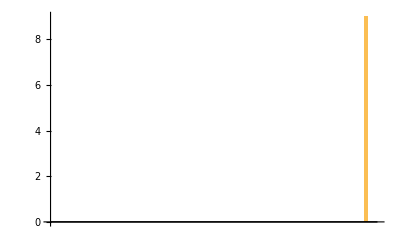

```mathematica
BarChart[run[[-5,1]]]
```